A funcao random gera aleatorios, faça f1 para ver sobre.

```mathematica
RandomInteger[{0,10}, 10]
```

{1,7,9,10,10,1,5,1,7,5}

Funcao Table
Table [ <expressao>, {<variavel>, <inicio>, <fim>, <passo>}]

```mathematica
Table[i^2, {i, 1, 10, 1}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[i^2, {i, 1, 10, 2}]
```

{1,9,25,49,81}

```mathematica
Table [i*(2+i), {i, 2,-4, -2}]
```

```mathematica
{8,0,0,8}
```

```mathematica
tab = Table[{i, i^2+1}, {i, 0, 10, 1}]
```

{{0,1},{1,2},{2,5},{3,10},{4,17},{5,26},{6,37},{7,50},{8,65},{9,82},{10,101}}

Pode fazer graficos descontinuos tbm:

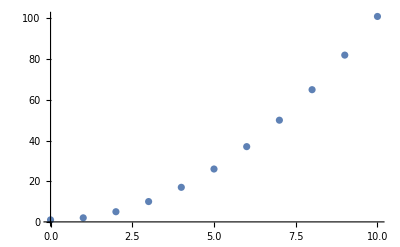

```mathematica
ListPlot[tab]
```

Da pra usar mais iteradores tbm,:

```mathematica
Table[i+j, {i, 1, 4, 1}, {j, 0, 3, 1}]
```

{{1,2,3,4},{2,3,4,5},{3,4,5,6},{4,5,6,7}}

Cada lista é o i, com j variando, entao na primeira lista i vale 0, e j varia de 0 a 3, na segunda lista i vale1, e j varia de 0 a 3, e etc

```mathematica
Table[i*j, {i, 1, 3}, {j, 1, i}]
```

{{1},{2,4},{3,6,9}}

```mathematica
Column[Table[i*j, {i, 1, 3}, {j, 1, i}]]
```

{1}
{2,4}
{3,6,9}

```mathematica
Column[Table[i*j, {i, 1, 3}, {j, 1, i}], Center]
```

{1}
{2,4}
{3,6,9}